```mathematica
<<Local`QFTToolKit`
QCDBaseIndices
Put[SaveFile=NBname["stub"]<>".out"]
```

{{0,1,2,3},{field,{1,2,3,4}},{feyn,{1,2,3,4,5}},{space,{1,2,3}},{timespace,{0,1}},{groupR,{1,2,3}},{gaugeG,{1,2,3,4,5,6,7,8}},{color,{1,2,3}},{flavor,{1,2,3,4,5,6}},{family,{1,2,3}}}

```mathematica
DefineTensorShortcuts[{{η,t,δ,ε,λ,D,F,U,H,g,τ,v,H,m,μ,n,Q,V,W},1},
{{T,U},2},
{{σ,λ,T},3},
{{σ},4}
]
```

VII.1 Electroweak Unification

```mathematica
PR1["VII.2.1: Unfortunately, the mass of the elusive Higgs particle H depends on the parameters in the double well potential ",V->-μ^2 SuperDagger[φ] . φ+λ(SuperDagger[φ].φ)^2," responsible for the spontaneous symmetry breaking.  Assuming that H is massive enough to decay into ",{Wu["+"],Wu["-"]},and,{Z,Z},", determine the rates for H to decay into various modes.",NL,
"VII.2.2: Show that it is possible to stay with the SU[2] gauge group and to identify W^3 as the photon A, but at the cost of inventing some experimentally unobserved lepton fields.  This theory does not describe our world: For one thing, it is essentially imposssible to incorporate the quarks.  Show this! Hint: We have to put the leptons into a triplet of SU[2] instead of a doublet."
]
```

VII.2.1: Unfortunately, the mass of the elusive Higgs particle H depends on the parameters in the double well potential V→-μ^2 φ^†.φ+λ (φ^†.φ)^2 responsible for the spontaneous symmetry breaking.  Assuming that H is massive enough to decay into {W_+^+,W_-^-} and {Z,Z}, determine the rates for H to decay into various modes.
VII.2.2: Show that it is possible to stay with the SU[2] gauge group and to identify W^3 as the photon A, but at the cost of inventing some experimentally unobserved lepton fields.  This theory does not describe our world: For one thing, it is essentially imposssible to incorporate the quarks.  Show this! Hint: We have to put the leptons into a triplet of SU[2] instead of a doublet.

General graphic definitions for array points and lines.

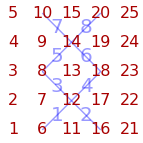

```mathematica
{vx,line}=GraphicPointLines[5,5,{{6,12},{16,12},{12,8},{12,18},{8,14},{18,14},{14,10},{14,20}}];
```

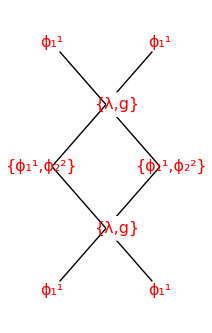

```mathematica
Graphics[{Thin,Black,Map[Line[#]&,line],
TextOver[ϕd[1],vx[[16]]],
TextOver[ϕd[1],vx[[6]]],
TextOver[ϕd[1],vx[[10]]],
TextOver[ϕd[1],vx[[20]]],
TextOver[{ϕd[1],ϕd[2]},vx[[8]]+{-.2,0}],
TextOver[{ϕd[1],ϕd[2]},vx[[18]]+{.2,0}],
TextOver[{λ,g},vx[[12]]+{.2,0}],
TextOver[{λ,g},vx[[14]]+{.2,0}]
}
]
```